```mathematica
rules ={"00011","01011","10011","11000","11010","11001"};
Lvar = Table[2^x, {x, 5, 12}]
plots = {};
Do[data = Import["/home/vynie/Documents/PycharmProjects/gameoflife (cópia)/Output/ScriptOutput/"<>rules[[3]]<>"/rand/L_"<>ToString[Lvar[[j]]]<>"/0.5/s1.csv", HeaderLines->1];
data = data[[All, {1, 2}]];
datat = Select[data, #[[1]]>20&];
logData=Map[{N[Log[10,#[[1]]]],N[Log[10,#[[2]]]]}&,datat];
Print[Fit[logData, {1, x}, x]];
AppendTo[plots, ListLogLogPlot[datat,  PlotRange->All,AxesOrigin->{0, 0}, AxesLabel->{"t", "ρu"}, PlotLegends->{ToString[Lvar[[j]]]}, PlotStyle->RandomColor[]]];
, {j, 1, Length[Lvar]}];
```

{32,64,128,256,512,1024,2048,4096}

0

0

0

«1 more identical outputs»

-0.429589-0.772532 x

-0.437978-0.766889 x

-0.449097-0.760187 x

-0.451329-0.758937 x

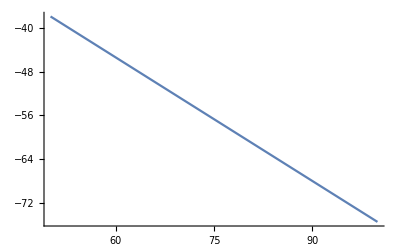

```mathematica
graph1 = Plot[-0.47567162945568886-0.7494657843484633 x, {x, 50, 100}]
```

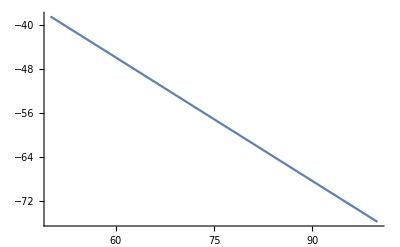

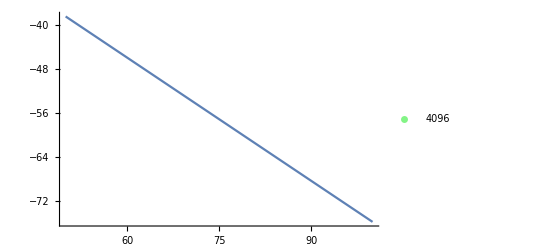

```mathematica
Show[graph1, plots[[8]]]
```

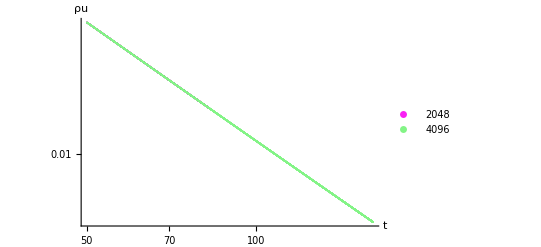

```mathematica
Show[plots, PlotRange->All]
```

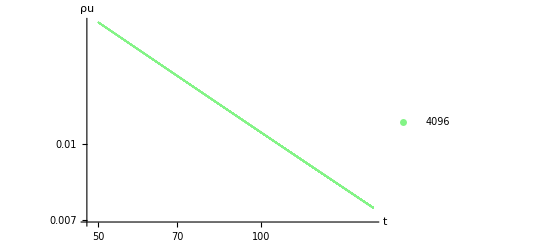
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{plots[[1]], plots[[3]]}, {plots[[2]], plots[[8]]}}]
```